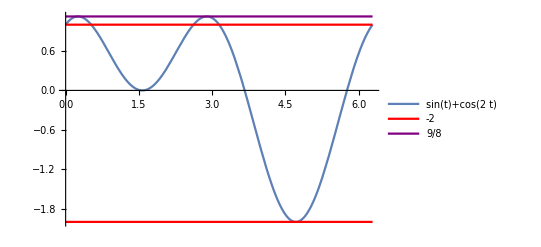

```mathematica
Plot[{Sin[t]+Cos[2*t],-2,1,9/8},{t,0,2*Pi},PlotLegends->"Expressions",PlotStyle->{Automatic,Red,Red,Purple}]
```

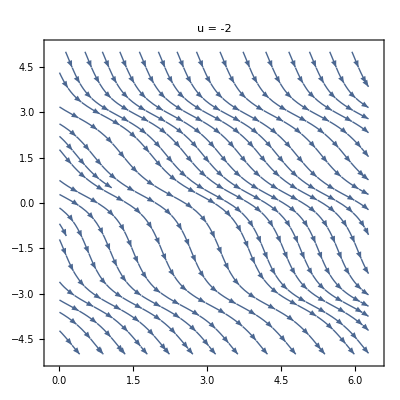

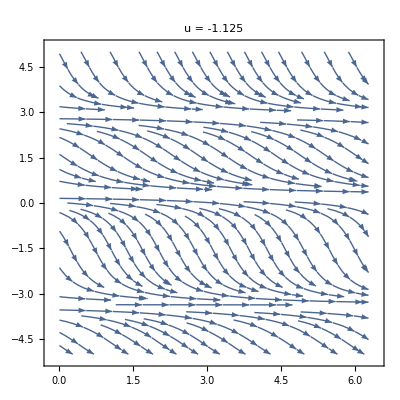

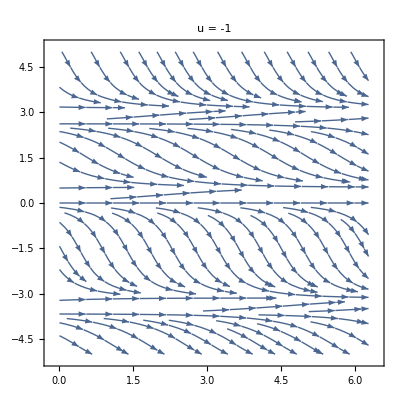

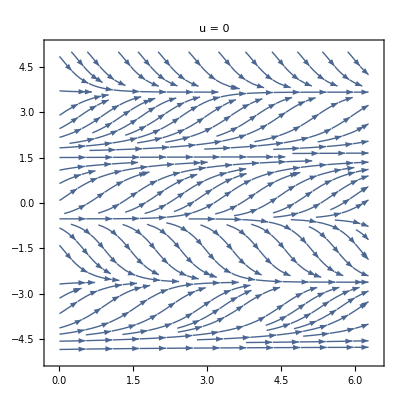

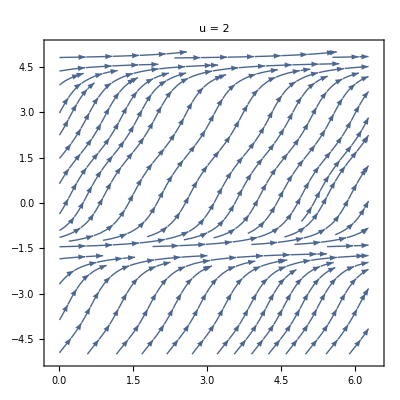

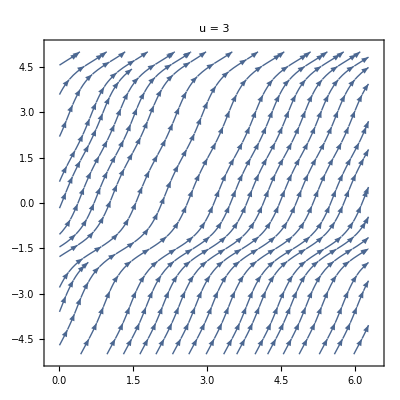

```mathematica
u=-2;StreamPlot[{1,u+Sin[x]+Cos[2*x]},{t,0,2*Pi},{x,-5,5},VectorScale->{Tiny},PlotLabel->"u = " <> ToString[u]]
u=-9/8;StreamPlot[{1,u+Sin[x]+Cos[2*x]},{t,0,2*Pi},{x,-5,5},VectorScale->{Tiny},PlotLabel->"u = " <> ToString[N[u]]]
u=-1;StreamPlot[{1,u+Sin[x]+Cos[2*x]},{t,0,2*Pi},{x,-5,5},VectorScale->{Tiny},PlotLabel->"u = " <> ToString[u]]
u=0;StreamPlot[{1,u+Sin[x]+Cos[2*x]},{t,0,2*Pi},{x,-5,5},VectorScale->{Tiny},PlotLabel->"u = " <> ToString[u]]
u=2;StreamPlot[{1,u+Sin[x]+Cos[2*x]},{t,0,2*Pi},{x,-5,5},VectorScale->{Tiny},PlotLabel->"u = " <> ToString[u]]
u=3;StreamPlot[{1,u+Sin[x]+Cos[2*x]},{t,0,2*Pi},{x,-5,5},VectorScale->{Tiny},PlotLabel->"u = " <> ToString[u]]
```

```mathematica
FullSimplify[Cos[4 ArcTan[4-√15]]+Sin[2 ArcTan[4-√15]]]
```

9/8

```mathematica
Sin[2*Pi]+Cos[4*Pi]
```

1

```mathematica
Solve[Sin[t]+Cos[2*t]==0,t]
```

{{t→ConditionalExpression[-(5 π)/6+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[-π/6+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]}}

```mathematica
Maximize[Sin[t]+Cos[2*t],t]
```

{Cos[4 ArcTan[4-√15]]+Sin[2 ArcTan[4-√15]],{t→2 ArcTan[4-√15]}}

```mathematica
Minimize[Sin[t]+Cos[2*t],t]
```

{-2,{t→(3 π)/2}}

```mathematica
Solve[D[Sin[t]+Cos[2*t],t]==0&&t>=0&&t≤2*Pi,t]
```

{{t→π/2},{t→(3 π)/2},{t→2 ArcTan[4-√15]},{t→2 ArcTan[4+√15]}}

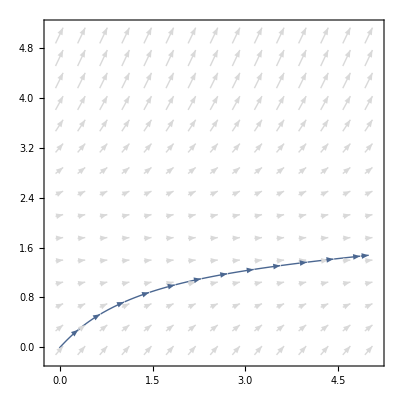
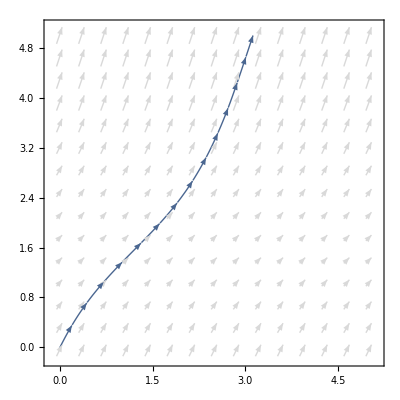

```mathematica
{VectorPlot[{1,1.1-Sin[p]},{t,-0.01,5},{p,-0.05,5},VectorScale->{Tiny},VectorStyle->LightGray,StreamStyle->Thin,StreamPoints->{{{{0,0},Automatic}}}]
,VectorPlot[{1,2-Sin[p]},{t,-0.01,5},{p,-0.05,5},VectorScale->{Tiny},VectorStyle->LightGray,StreamStyle->Thin,StreamPoints->{{{{0,0},Automatic}}}]}
```

```mathematica
Clear[p,x,t];s=NDSolve[{1.1-Sin[p[t]]==p'[t],p[0]==0},p[t],{t,0,2*Pi}]
```

{{p[t]→InterpolatingFunction[{{0., 6.28319}}, <>][t]}}

```mathematica
u=NDSolve[{2-Sin[q[t]]==q'[t],q[0]==0},q[t],{t,0,2*Pi}]
```

{{q[t]→InterpolatingFunction[{{0., 6.28319}}, <>][t]}}

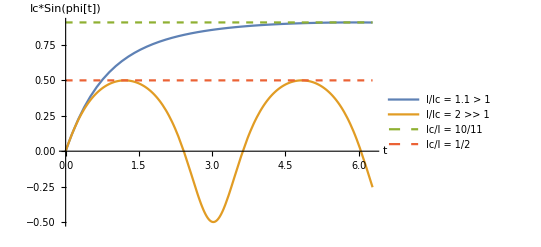

```mathematica
Plot[{10/11*Sin[Evaluate[p[t]/.s]],1/2*Sin[Evaluate[q[t]/.u]],10/11,1/2},{t,0,2*Pi},PlotStyle->{Automatic,Automatic,Dashed,Dashed},PlotLegends->{"I/Ic = 1.1 > 1","I/Ic = 2 >> 1","Ic/I = 10/11","Ic/I = 1/2"},AxesLabel->{"t","Ic*Sin(phi[t])"}]
```

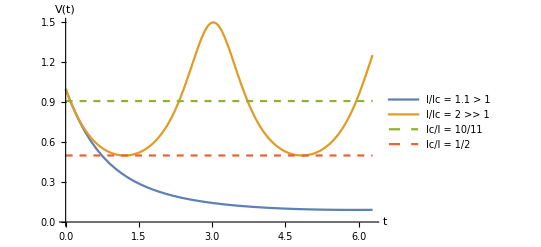

```mathematica
R=1;Plot[{R-10/11*R*Sin[Evaluate[p[t]/.s]],R-1/2*R*Sin[Evaluate[q[t]/.u]],10/11,1/2},{t,0,2*Pi},PlotStyle->{Automatic,Automatic,Dashed,Dashed},PlotLegends->{"I/Ic = 1.1 > 1","I/Ic = 2 >> 1","Ic/I = 10/11","Ic/I = 1/2"},AxesLabel->{"t","V(t)"}]
```

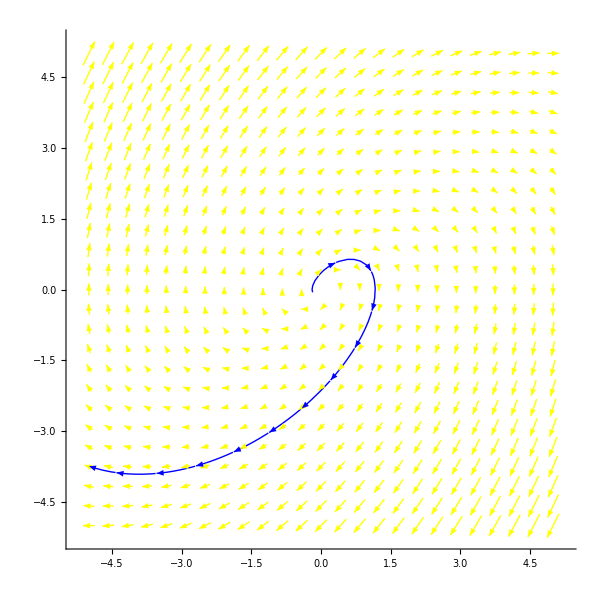

```mathematica
VectorPlot[{j,-r+j},{r,-5,5},{j,-5,5},VectorScale->{Tiny},VectorStyle->Yellow,StreamStyle->Blue,StreamPoints->{{{{1,.5},Automatic}}},Axes->True,Frame->None,VectorPoints->Fine]
```

```mathematica
A = {{0,1},{-1,1}}
```

{{0,1},{-1,1}}

```mathematica
Eigensystem[A]
```

{{1/2 (1+ⅈ √3),1/2 (1-ⅈ √3)},{{-1/2 ⅈ (ⅈ+√3),1},{1/2 ⅈ (-ⅈ+√3),1}}}

```mathematica
X[t_]={r[t],j[t]}
```

{r[t],j[t]}

```mathematica
system = X'[t]==A.X[t]
```

{r'[t],j'[t]}=={j[t],j[t]-r[t]}

```mathematica
sol=DSolve[{system,r[0]==x,j[0]==y},{r,j},t]
```

{{j→Function[{t},-1/3 ⅇ^(t/2) (-3 y Cos[(√3 t)/2]+2 √3 x Sin[(√3 t)/2]-√3 y Sin[(√3 t)/2])],r→Function[{t},1/3 ⅇ^(t/2) (3 x Cos[(√3 t)/2]-√3 x Sin[(√3 t)/2]+2 √3 y Sin[(√3 t)/2])]}}

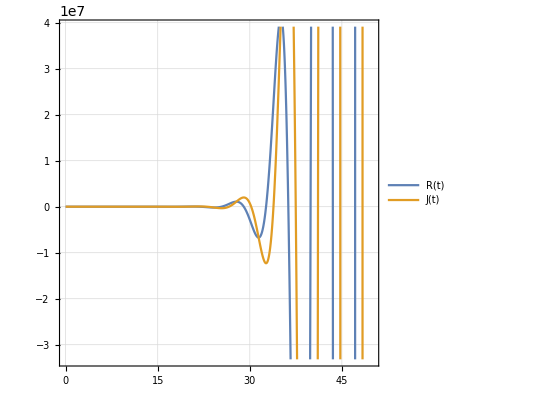

```mathematica
Plot[{-(2 ⅇ^(t/2) Sin[(√3 t)/2])/(√3),1/3 ⅇ^(t/2) (3 Cos[(√3 t)/2]-√3 Sin[(√3 t)/2])},{t,0,50},PlotTheme->"Detailed",PlotLegends->{"R(t)","J(t)"},AspectRatio->1]
```

```mathematica
Clear[a,b,R,J]
A = {{a,b},{-b,-a}};
Eigensystem[A]
Tr[A]
Det[A]
X[t_]={r[t],j[t]};
DSolve[{X'[t]==A.X[t],r[0]==R,j[0]==J},{r,j},t]
```

{{-√(a^2-b^2),√(a^2-b^2)},{{-(a-√(a^2-b^2))/b,1},{-(a+√(a^2-b^2))/b,1}}}

0

-a^2+b^2

```mathematica
Plot3D[{b^2-a^2,0},{a,-5,5},{b,-5,5},AxesLabel->{a,b,f}]
```

-Graphics3D-

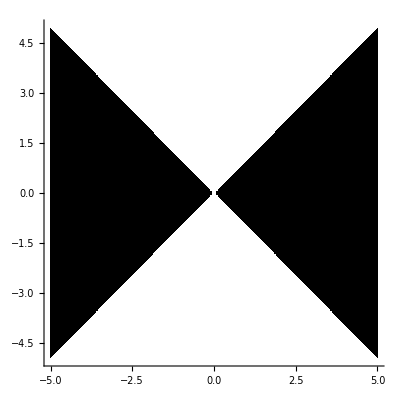

```mathematica
ContourPlot[{Sign[b^2-a^2]},{a,-5,5},{b,-5,5},Axes->True,Frame->False,ColorFunction->GrayLevel,FrameLabel->Automatic]
```

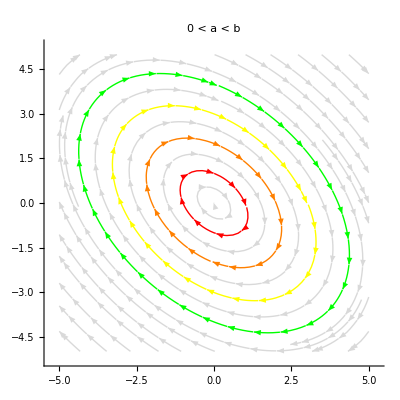

```mathematica
a=2;
b=5;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{1,0},Red},{{0,-2},Orange}, {{3,0},Yellow},{{0,4},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"0 < a < b"]
```

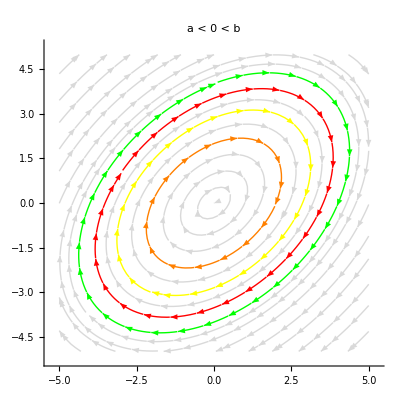

```mathematica
a=-2;
b=5;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,0},Orange}, {{-2,-3},Yellow},{{0,4},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"a < 0 < b"]
```

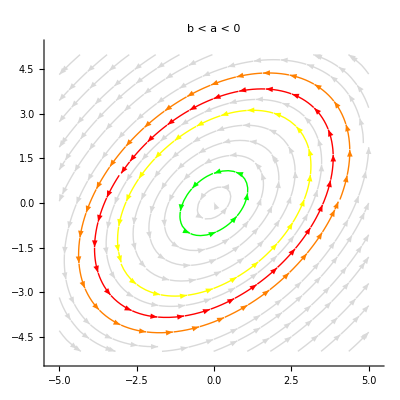

```mathematica
a=2;
b=-5;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{4,0},Orange}, {{-3,-2},Yellow},{{0,1},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"b < a < 0"]
```

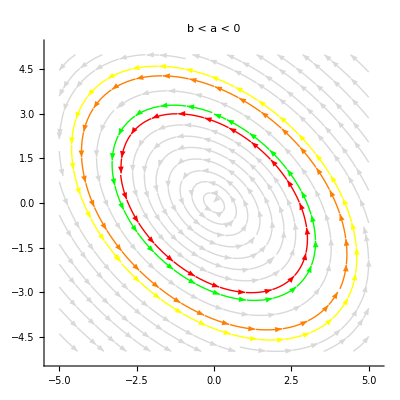

```mathematica
a=-2;
b=-5;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{4,-3},Orange}, {{-3,-2},Yellow},{{0,3},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"b < a < 0"]
```

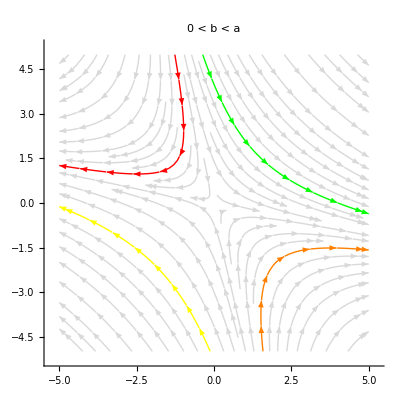

```mathematica
a=5;
b=2;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-2},Orange}, {{-2,-2},Yellow},{{0,4},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"0 < b < a"]
```

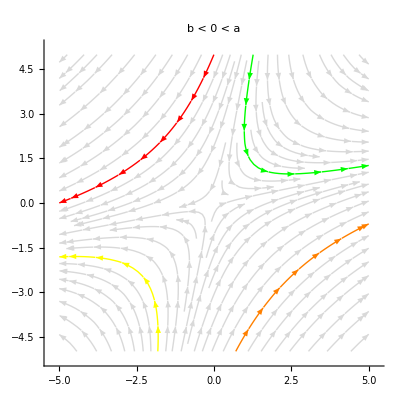

```mathematica
a=5;
b=-2;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-3,-2},Yellow},{{1,2},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"b < 0 < a"]
```

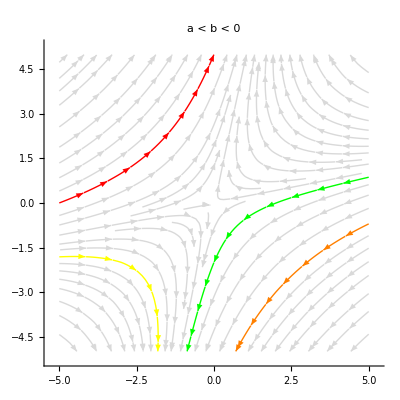

```mathematica
a=-5;
b=2;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-3,-2},Yellow},{{0,-2},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"a < b < 0"]
```

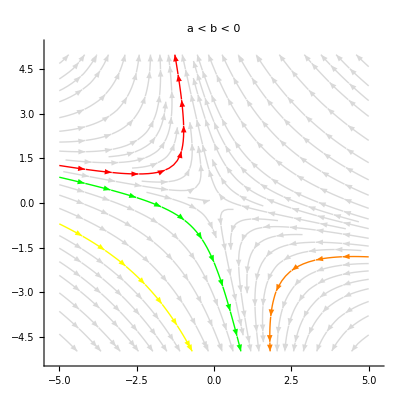

```mathematica
a=-5;
b=-2;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-3,-2},Yellow},{{0,-2},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"a < b < 0"]
```

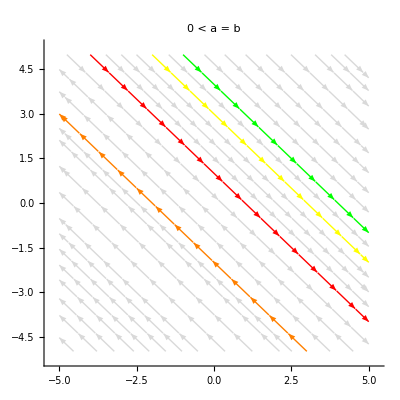

```mathematica
a=2;
b=2;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{1,0},Red},{{0,-2},Orange}, {{3,0},Yellow},{{0,4},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"0 < a = b"]
```

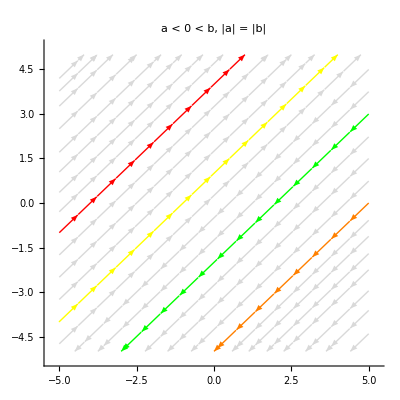

```mathematica
a=-2;
b=2;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-3,-2},Yellow},{{0,-2},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"a < 0 < b, |a| = |b|"]
```

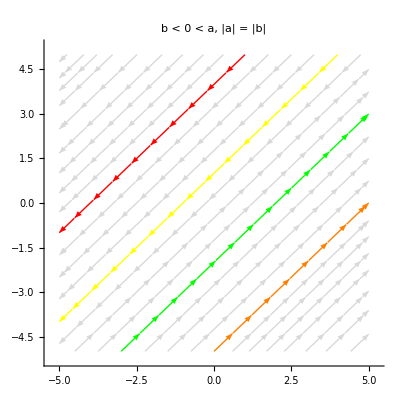

```mathematica
a=2;
b=-2;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-3,-2},Yellow},{{0,-2},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"b < 0 < a, |a| = |b|"]
```

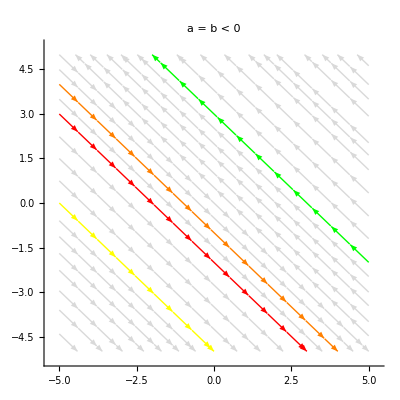

```mathematica
a=-2;
b=-2;
VectorPlot[{a*r+b*j,-b*r+-a*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-3,-2},Yellow},{{0,3},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"a = b < 0"]
```

```mathematica
Clear[a,b,R,J]
A = {{0,0},{a,b}};
Eigensystem[A]
Tr[A]
Det[A]
X[t_]={r[t],j[t]};
DSolve[{X'[t]==A.X[t],r[0]==R,j[0]==J},{r,j},t]
```

{{0,b},{{-b/a,1},{0,1}}}

b

0

{{j→Function[{t},(b ⅇ^(b t) J-a R+a ⅇ^(b t) R)/b],r→Function[{t},R]}}

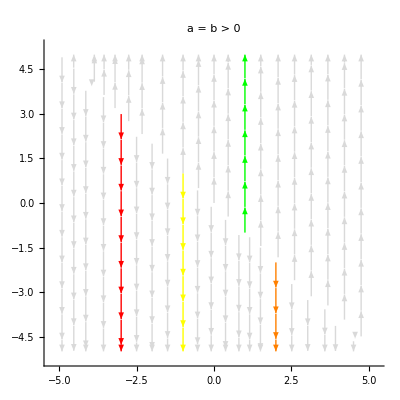

```mathematica
a=1;
b=1;
VectorPlot[{0,a*r+b*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-1,-2},Yellow},{{1,3},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"a = b > 0"]
```

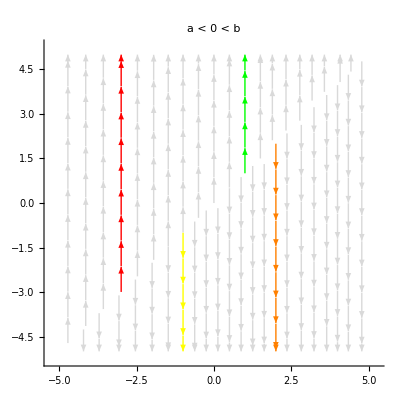

```mathematica
a=-1;
b=1;
VectorPlot[{0,a*r+b*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-1,-2},Yellow},{{1,3},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"a < 0 < b"]
```

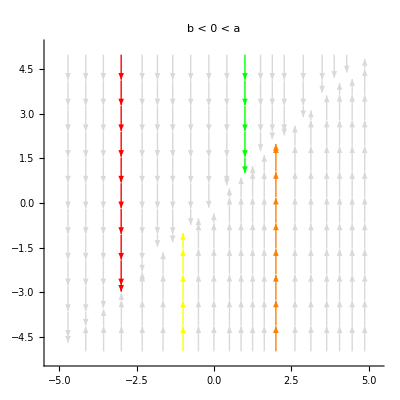

```mathematica
a=1;
b=-1;
VectorPlot[{0,a*r+b*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-1,-2},Yellow},{{1,3},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"b < 0 < a"]
```

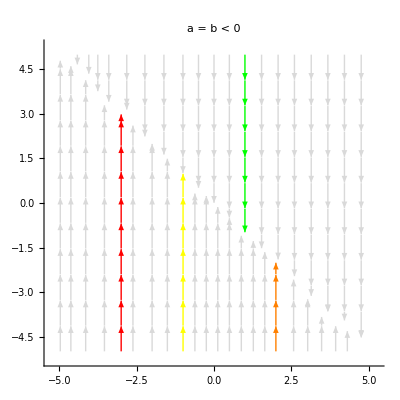

```mathematica
a=-1;
b=-1;
VectorPlot[{0,a*r+b*j},{r,-5,5},{j,-5,5} ,VectorScale->{Tiny},VectorStyle->None,StreamStyle->LightGray,StreamPoints->{{{{-3,1},Red},{{2,-3},Orange}, {{-1,-2},Yellow},{{1,3},Green},Automatic}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"a = b < 0"]
```

```mathematica
DSolve[{e*x''[t]+x'[t]+x[t]==0,x[0]==1,x'[0]==0},x[t],t]
```

{{x[t]→1/(2 √(1-4 e))(-ⅇ^(((-1-√(1-4 e)) t)/(2 e))+√(1-4 e) ⅇ^(((-1-√(1-4 e)) t)/(2 e))+ⅇ^(((-1+√(1-4 e)) t)/(2 e))+√(1-4 e) ⅇ^(((-1+√(1-4 e)) t)/(2 e)))}}

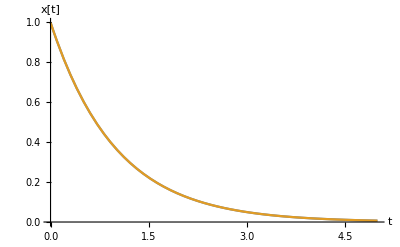

```mathematica
e=0.0001;Plot[{1/(2 √(1-4 e))(-ⅇ^(((-1-√(1-4 e)) t)/(2 e))+√(1-4 e) ⅇ^(((-1-√(1-4 e)) t)/(2 e))+ⅇ^(((-1+√(1-4 e)) t)/(2 e))+√(1-4 e) ⅇ^(((-1+√(1-4 e)) t)/(2 e))),E^(-t)},{t,0,5},AxesLabel->{"t","x[t]"}]
```

```mathematica
DSolve[{t'[x]==1-Sin[t[x]],t[0]==2},t[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{t[x]→2 ArcCos[-((2+x+(2 (1-Cos[1]^2+Cos[1] √(1-Cos[1]^2)))/(-1+2 Cos[1]^2))/(√(4+4 x+2 x^2+(8 (1-Cos[1]^2+Cos[1] √(1-Cos[1]^2)))/(-1+2 Cos[1]^2)+(8 x (1-Cos[1]^2+Cos[1] √(1-Cos[1]^2)))/(-1+2 Cos[1]^2)+(8 (1-Cos[1]^2+Cos[1] √(1-Cos[1]^2))^2)/((-1+2 Cos[1]^2)^2))))]},{t[x]→2 ArcCos[(2+x-(2 (-1+Cos[1]^2+Cos[1] √(1-Cos[1]^2)))/(-1+2 Cos[1]^2))/(√(4+4 x+2 x^2-(8 (-1+Cos[1]^2+Cos[1] √(1-Cos[1]^2)))/(-1+2 Cos[1]^2)-(8 x (-1+Cos[1]^2+Cos[1] √(1-Cos[1]^2)))/(-1+2 Cos[1]^2)+(8 (-1+Cos[1]^2+Cos[1] √(1-Cos[1]^2))^2)/((-1+2 Cos[1]^2)^2)))]}}

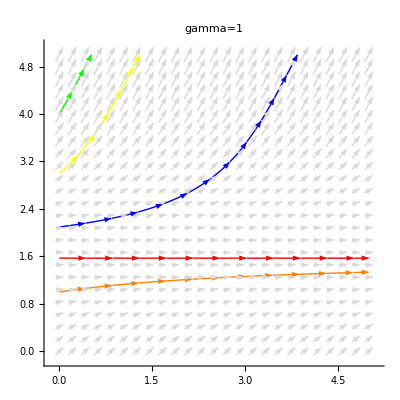

```mathematica
VectorPlot[{1,1-Sin[t]},{x,0,5},{t,0,5},VectorScale->{Tiny},VectorStyle->LightGray,StreamStyle->Blue,StreamPoints->{{{{0,Pi/2},Red},{{0,1},Orange}, {{0,3},Yellow}, {{0,3/2},Blue},{{0,4},Green}}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"gamma=1"]
```

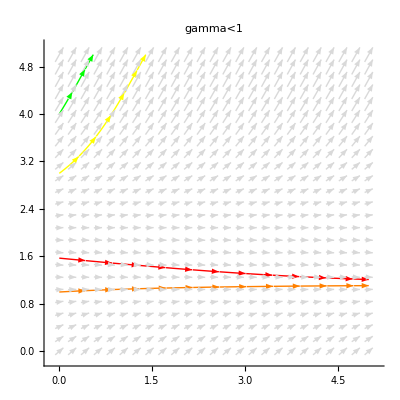

```mathematica
VectorPlot[{1,0.9-Sin[t]},{x,0,5},{t,0,5},VectorScale->{Tiny},VectorStyle->LightGray,StreamStyle->Blue,StreamPoints->{{{{0,Pi/2},Red},{{0,1},Orange}, {{0,3},Yellow}, {{0,3/2},Blue},{{0,4},Green}}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"gamma<1"]
```

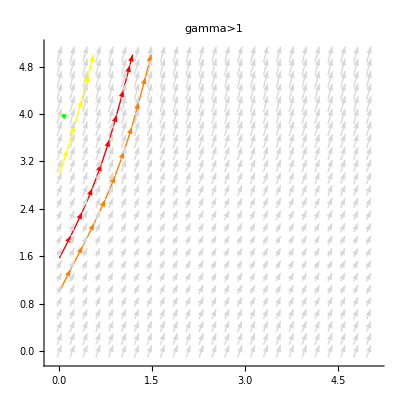

```mathematica
VectorPlot[{1,3-Sin[t]},{x,0,5},{t,0,5},VectorScale->{Tiny},VectorStyle->LightGray,StreamStyle->Blue,StreamPoints->{{{{0,Pi/2},Red},{{0,1},Orange}, {{0,3},Yellow}, {{0,3/2},Blue},{{0,4},Green}}},Axes->True,Frame->None,VectorPoints->Fine,PlotLabel->"gamma>1"]
```

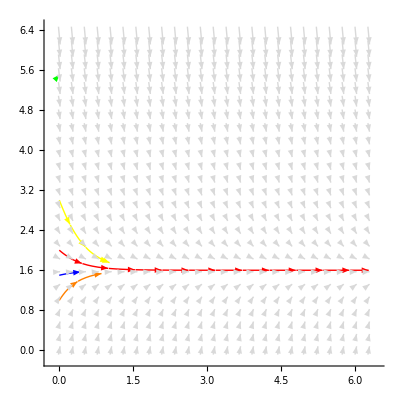

```mathematica
VectorPlot[{1,5-2.5*t-Sin[t]},{x,0,2*Pi},{t,0,2*Pi},VectorScale->{Tiny},VectorStyle->LightGray,StreamStyle->Blue,StreamPoints->{{{{0,2},Red},{{0,1},Orange}, {{0,3},Yellow}, {{0,3/2},Blue},{{0,5.5},Green}}},Axes->True,Frame->None,VectorPoints->Fine]
```